NDSolve::deqn: Equation or list of equations expected instead of -19.6\ Sin[ϕ[t]] in the first argument {-19.6\ Sin[ϕ[t]], π/9, 0}.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-19.6\ Sin[ϕ[0.000408571]], π/9, 0}, ϕ, {0.000408571, 0, 20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-19.6\ Sin[ϕ[0.000408571]], 0.349066, 0.}, ϕ, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.408572 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{-19.6\ Sin[ϕ[0.408572]], π/9, 0}, ϕ, {0.408572, 0, 20}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

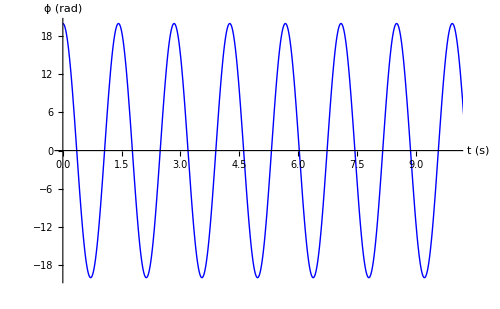
show -Graphics-

```mathematica
g = 9.8;
l = 0.5;
omega = √(g/l);

ϕ0 = 20 * Pi/180;
ω0 = 0;

ode1 = {ϕ ' '[t] = - (g/l) * Sin[ϕ[t]], ϕ[0] = ϕ0, ϕ'[0] = ω0};
sol = NDSolve[ode1, ϕ, {t,0,20}];

approx = (180/Pi) ϕ0 Cos[omega * t];

myplot = Plot[{approx, (180/Pi) ϕ[t]/. sol}, {t,0,20},PlotStyle -> {{Blue}, {Dashed, Red}},
AxesLabel -> {"t (s)", "ϕ (rad)"},
PlotRange -> {{0,10}, {-20,20}}, ImageSize -> {500,300}];
show(myplot)
```